```mathematica
Clear["Global`*"]
```

```mathematica
ρ=2040.;
cv=2051.;
sv=1423.;
μ=ρ*sv*sv;
λ=ρ*cv*cv-2*μ;
(*a=-5011.*10^9;
b=-1692.*10^9;
c=-158.*10^9;拟合系数 a b c*)
v1=2*c;
v2=b;
v3=a/4;
c111=v1+6*v2+8*v3;
c112=v1+2*v2;
c144=v2;
c155=v2+2*v3;
e11=-(x λ+x μ)/(μ (3 λ+2 μ))*10^6;e22=(x λ)/(2 μ (3 λ+2 μ))*10^6;e33=(x λ)/(2 μ (3 λ+2 μ))*10^6;
```

```mathematica
A1313=μ+c155*e11+c144*e22+c155*e33;
```

```mathematica
A2323=μ+c144*e11+c155*e22+c155*e33;
```

```mathematica
A3333=λ+2*μ+c112*e11+c112*e22+c111*e33;
```

```mathematica
x1={0,0.3141,0.7958,1.2984,1.801,2.2932,2.8063,3.2984,3.7906,4.3037,4.7958};
Vp={2051,2052.6,2065.3,2084.2,2099.9,2115.7,2128.3,2140.9,2150.4,2163,2172.5};
```

```mathematica
x2={0.02887,0.315470,0.807591,1.309132,1.82387,2.310332,2.828853,3.326623,3.809314,4.310854,4.81617};
Vs13={1428.99437,1446.06343,1485.89125,1520.02938,1545.06401,1575.21936,1593.42636,1613.34027,1635.53006,1652.59912,1665.68541};
```

```mathematica
x3={0.31547,0.81324,1.3129,1.8201,2.3141,2.81942,3.31908,3.81874,4.31651,4.80863};
Vs23={1425.58056,1432.97715,1443.21859,1457.44281,1468.25322,1477.92569,1487.59816,1494.42578,1501.82238,1508.65001};
```

```mathematica
(*拟合表达式分别为eqn1:vp=√(A3333/ρ);  eqn2:vs13=√(A1313/ρ);  eqn3:vs23=√(A2323/ρ);*)
```

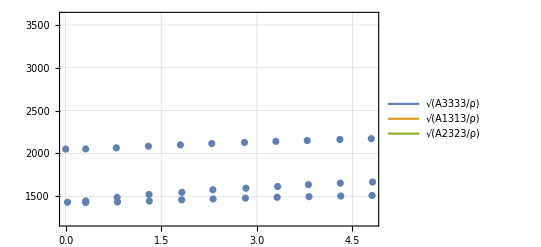

```mathematica
Show[{Plot[{√(A3333/ρ),√(A1313/ρ),√(A2323/ρ)},{x,0,6},PlotTheme->"Detailed"],ListPlot[{x1,Vp}//Transpose,PlotTheme->"Detailed"],ListPlot[{x2,Vs13}//Transpose,PlotTheme->"Detailed"],ListPlot[{x3,Vs23}//Transpose,PlotTheme->"Detailed"]},PlotRange->{1200,3600}]
```